```mathematica
(* y''-2y'+y=0 *)
```

#### Equação característica

```mathematica
Solve[λ^2-2λ+1==0,λ]
```

{{λ→1},{λ→1}}

```mathematica
sh[x_]:=c1 ⅇ^x+x c2 ⅇ^x
```

```mathematica
(* Condições: y(0)==3 e y'(0)==1 *)
```

```mathematica
Solve[{sh[0]==3,(D[sh[x],x]/.x->0)==1},{c1,c2}]
```

{{c1→3,c2→-2}}

```mathematica
shf[x_]=sh[x]/.c1->3/.c2->-2
```

3 ⅇ^x-2 ⅇ^x x

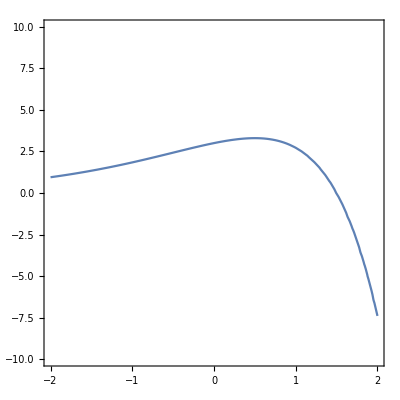

```mathematica
ContourPlot[y==shf[x],{x,-2,2},{y,-10,10}]
```

```mathematica
graphs=Table[ContourPlot[y==3 ⅇ^x+c2 ⅇ^x x,{x,-2,2},{y,-10,10},ContourStyle->{Thin,RGBColor[0,0,0]}],{c2,-6,6}];
```

```mathematica
γ[x_]:={x,3 ⅇ^x+-2 ⅇ^x x}
```

```mathematica
α[x_]:={x,3 ⅇ^x+-6 ⅇ^x x}
```

```mathematica
β[x_]:={x,3 ⅇ^x+6 ⅇ^x x}
```

```mathematica
g1=Manipulate[Show[graphs,Graphics[{Red,Point[{γ[x],α[x],β[x]}]}],Graphics[{Red,Arrow[{γ[x],γ[x]+.4γ'[x]}]}],Graphics[{Red,Arrow[{α[x],α[x]+.4α'[x]}]}],Graphics[{Red,Arrow[{β[x],β[x]+.4β'[x]}]}]],{x,-2,2}]
```

```mathematica
Export["g1.gif",g1]
```

g1.gif

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["g1.gif"]]]
```